1. Renormalization Group Recursive Equations Setup

```mathematica
Clear[μ,η,y]
dim=8;
y=1;
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x1*x3+y*x0*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0≤1,x0+=2,For[x2=-1,x2≤1,x2+=2,For[x4=-1,x4≤1,x4+=2,leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];]]]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4]==leq[4];
req[5]==leq[5];
req[6]==leq[6];
req[7]==leq[7];
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0][[1]];
SB[0]={B[0]->2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0&&B[2]>0&&B[4]>0&&B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0&&B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0&&B[5]>0&&B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[5]],1]];
SBT=Table[Part[SB[n],1],{n,0,5}];
```

2. One- and Two-Point Function Setup

```mathematica
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->μ^(y),B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[D[(B[i]/.SBT),A[j]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
Ω=Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
InitRGΩ:=Block[{},
InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];
This is all zero,anyway!*)
];
RGΩ:=Block[{},
Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;
];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

3. One Point Functions: IE and Mag

3.1 Internal Energy

```mathematica
Clear[μ,η,IE,IEc]
InitRGW;
(**Temperature for Mag, IE**)
precN=1000;
Tmin=0.011;
Tmax=10.006;
Tinc=0.005;
TVector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv];
(*kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};*)
kVector=Range[6,9,1];
InitRGW;
dμdβ=-4 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=N[1.0,precN];
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[TVector][[1]]}];
μind=0;
Do[kind=1;
μind++;
Clear[μ];
InitRGW;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],Part[Part[IE,kind],μind]=N[1/(2^(i)+1)*(dA0dμ.Υ).(DLnZ1/.SAT),precN];kind++,];],
{Tx,1,Dimensions[μVector][[1]],1}
];
Rasterize[ListLinePlot[Table[Table[{1.0/μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick]]
IEc=IE;
PrependTo[IEc,TVector];
PrependTo[IEc,1.0/μVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
IEc=Transpose[IEc];
IEc=PrependTo[IEc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_IE_test.csv",IEc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_IE_test.csv",IEc](*For Windows*)*)
```

-Graphics-

3.2 Magnetization vs H (big)

```mathematica
(*μ=4.85165*10^8;T=0.1;
μ=22026.5;       T=0.2;
μ=54.5982;       T=0.5;
μ=7.38906;       T=1.0;
μ=3.0;           T=1.82048;
μ=2.71828;       T=2.0;
μ=1.49182;       T=5;
μ=1.2214;        T=10;
μ=1.0;           T=10^9; 
*)
```

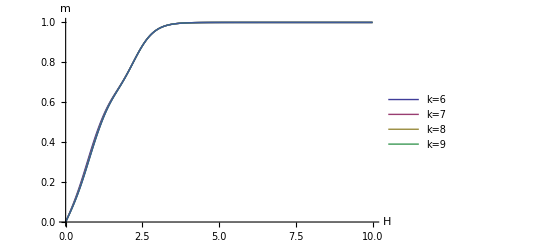

```mathematica
(* μ=7.389; T=1.0 *)
Clear[μ,η,MagHc]
InitRGW;
precN=1000;
kVector=Range[6,10,1];
InitRGW;
μ=N[7.389,100];(*1:high T;1000:low T*)
Hmin=0;
Hmax=10;
Hinc=0.01;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=N[Exp[-Hmin],precN];
ηmin=N[Exp[-Hmax],precN];
ηVector=N[Exp[-HVector],precN];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H*)
InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=N[ηVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=N[1/(2^(j+1)+1)*(dA0dη.Υ).(DLnZ1/.SAT),precN];kind++,];
];
];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_magH_m7d389_test.csv",MagHc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_magH_m7d389_test.csv",MagHc](*For Windows*)*)
```

3.3 Magnetization vs H (small)

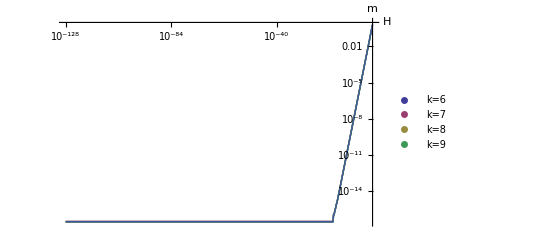

```mathematica
(*μ=3*)
Clear[μ,η,MagHc];
precN=1000;(*1000*)
HVector=Range[1,0.1,-0.025];
HVector=Join[HVector,Range[0.1-0.0025,0.01,-0.0025]];
HVector=Join[HVector,Range[0.01-0.00025,0.001+0.00025,-0.00025]];
HVector=Join[HVector,10^Range[-3,-64,-0.25]];
HVector=Join[HVector,10^Range[-64.5,-128,-0.5]];
HVecotr=N[HVector,precN];
ηVector=N[Exp[-HVector],precN];
kVector=Range[6,10,1]; (*Range[6,128,1];*)
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];
InitRGW;
dηdH=-2 η;
kind=1;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
μ=3;
Clear[η];
kind=1;
InitRGW;
η=N[ηVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=N[1/(2^(j+1)+1)*(dA0dη.Υ).(DLnZ1/.SAT),precN];
kind++,
];
];
];
ListLogLogPlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},Joined->True,AxesLabel->{"H","m"}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,N[ηVector,15]];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_magHz2_m3_test.csv",MagHc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_magHz2_m3_test.csv,MagHc](*For Windows*)*)
```

3.4 Magnetization vs μ 
<m> vs μ at different H

H=1.×10^-8; η=0.99999999

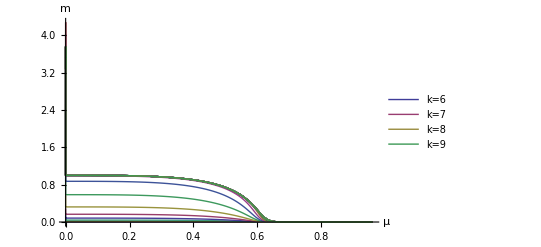

```mathematica
(*H=1e-8*)
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
H=1/10^8;
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=Range[Tmin,Tmax,Tinc];
TVector=N[Join[TVector,Range[10.5,50,0.5]],precN];
μVector=N[Exp[-2/TVector],precN];
kVector=Range[6,64,1];
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6],"; η=",N[η,10]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[Magμ,kind],i]=N[1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),20];++kind,];];];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"μ","m"},PlotRange->Full]
Magμc=Magμ;
kVectorc=kVector;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,15]];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_FM_magm_H1e-8.csv",Magμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_magm_H1e-2_test.csv,Magμc](*For Windows*)*)
```

4. Two Point Functions : Cv and χ

4.1 Specific Heat Cv

0.3322 Completed.

PrependTo::normal: Nonatomic expression expected at position 1 in PrependTo[χμc, {0.01, 0.06, 0.11, 0.16, 0.21, 0.26, 0.31, 0.36, 0.41, 0.46, 0.51, 0.56, 0.61, 0.66, 0.71, 0.76, 0.81, 0.86, 0.91, 0.96, « 11 », 1.56, 1.61, 1.66, 1.71, 1.76, 1.81, 1.86, 1.91, 1.96, 2.01, 2.06, 2.11, 2.16, 2.21, 2.26, 2.31, 2.36, 2.41, 2.46, « 251 »}].

PrependTo::normal: Nonatomic expression expected at position 1 in PrependTo[χμc, {1.3839×10^-87, 3.33824×10^-15, 1.2698×10^-8, 3.72665×10^-6, 0.0000730907, 0.000456324, 0.00157797, 0.00386592, 0.00761185, 0.0129349, 0.01981, « 29 », 0.369714, 0.378752, 0.387567, 0.396164, 0.404551, 0.412732, 0.420714, 0.428503, 0.436104, 0.443522, « 251 »}].

Transpose::list: List expected at position 2 in Transpose[{0, 0, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, 51, 52, 53, « 11 »}, χμ].

0.6645 Completed.

PrependTo::normal: Nonatomic expression expected at position 1 in PrependTo[χμc, {0.01, 0.06, 0.11, 0.16, 0.21, 0.26, 0.31, 0.36, 0.41, 0.46, 0.51, 0.56, 0.61, 0.66, 0.71, 0.76, 0.81, 0.86, 0.91, 0.96, « 11 », 1.56, 1.61, 1.66, 1.71, 1.76, 1.81, 1.86, 1.91, 1.96, 2.01, 2.06, 2.11, 2.16, 2.21, 2.26, 2.31, 2.36, 2.41, 2.46, « 251 »}].

General::stop: Further output of PrependTo :: normal will be suppressed during this calculation.

Transpose::list: List expected at position 2 in Transpose[{0, 0, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, 51, 52, 53, « 11 »}, χμ].

0.9967 Completed.

Transpose::list: List expected at position 2 in Transpose[{0, 0, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, 51, 52, 53, « 11 »}, χμ].

General::stop: Further output of Transpose :: list will be suppressed during this calculation.

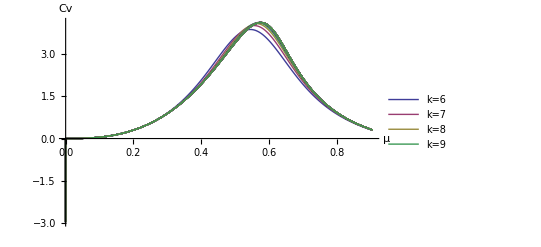

```mathematica
Clear[η,μ,y,Cvμc]
InitRGΩ;
y=1;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=N[1.0,1000];
(**Temperature for Cv, X**)
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.05;
TVector=Range[Tmin,Tmax,Tinc];
TVector=N[Join[TVector,Range[10.1,20,0.1]],precN];
μVector=N[Exp[-2/TVector],precN];
kVector=Range[6,64,1];
Cvμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(*Magnetization at different H at μ=0.01*);
μind=0;
Do[kind=1;
μind++;
If[Mod[μind,100]==0,Print[N[μind/Dimensions[μVector][[1]],4]," Completed."];
Clear[χμc,kVectorc];
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_FM_Cv_pre.csv",Cvμc];(*For Linux*)
];
Clear[μ];
InitRGΩ;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=N[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ,precN];
term1=N[d2μdβ2*(dA0dμ.Υ).DlnZ,precN];
term2=N[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ),precN];
term3=N[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ),precN];
Part[Part[Cvμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1)/TVector[[μind]],precN];
kind++,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
ListLinePlot[Table[Table[{μVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
Cvμc=Cvμ;
PrependTo[Cvμc,TVector];
PrependTo[Cvμc,μVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_FM_Cv_pre.csv",Cvμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_Cv_v2.csv,Cvμc](*For Windows*)*)
```

4.2 Susceptibility χ

0.3322 Completed.

0.6645 Completed.

0.9967 Completed.

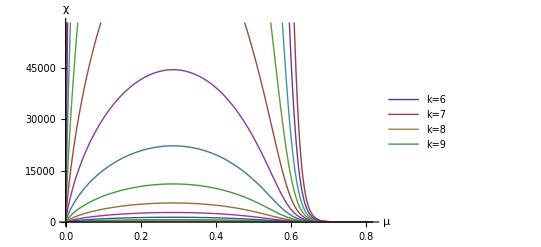

```mathematica
(************************* χ at H=0 ****************************)
Clear[η,μ,y,χμ,χμc]
y=1;
H=0;
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.05;
TVector=Range[Tmin,Tmax,Tinc];
TVector=N[Join[TVector,Range[10.1,20,0.1]],precN];
μVector=N[Exp[-4/TVector],precN];
kVector=Range[6,20,1];
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
If[Mod[μind,100]==0,
Print[N[μind/Dimensions[μVector][[1]],4]," Completed."];
Clear[χμc,kVectorc];
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive//Research/AntiHN/Maca/data/HN5_FM_X_pre.csv",χμc],(*For Windows*)
];
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=N[(dηdH)^2*(d2A0dη2.Υ).DlnZ,precN];
term1=N[d2ηdH2*(dA0dη.Υ).DlnZ,precN];
term2=N[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη),precN];
term3=N[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ),precN];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20]*μVector[[μind]]*4/TVector[[μind]];
++kind,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_FM_X_pre.csv",χμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_X_H0.csv",χμc](*For Windows*)*)
```

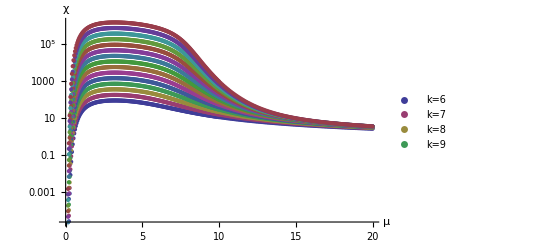

```mathematica
ListLogPlot[Table[Table[{TVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
```

```mathematica
μVector
```

{1.91517×10^-174,1.11438×10^-29,1.6124×10^-16,1.38879×10^-11,5.34225×10^-9,2.08232×10^-7,2.49001×10^-6,0.0000149453,0.0000579403,0.000167312,0.000392436,0.00079049,0.0014196,0.00233299,0.00357495,0.00517892,0.00716698,0.00955049,0.0123314,0.0155039,0.0190556,0.0229696,0.0272254,0.0318004,0.0366704,0.0418107,0.0471965,0.0528036,0.0586083,0.064588,0.0707214,0.0769882,0.0833696,0.0898478,0.0964065,0.103031,0.109707,0.116422,0.123164,0.129923,0.136689,0.143453,0.150208,0.156946,0.163662,0.170348,0.177001,0.183615,0.190186,0.196712,0.203188,0.209611,0.215981,0.222293,0.228547,0.23474,0.240872,0.246942,0.252948,0.25889,0.264767,0.270579,0.276326,0.282007,0.287623,0.293173,0.298657,0.304076,0.309431,0.314721,0.319947,0.325109,0.330208,0.335244,0.340219,0.345131,0.349984,0.354776,0.359508,0.364182,0.368798,0.373356,0.377858,0.382304,0.386695,0.391032,0.395314,0.399544,0.403722,0.407848,0.411923,0.415949,0.419925,0.423853,0.427733,0.431565,0.435352,0.439092,0.442788,0.446439,0.450047,0.453612,0.457134,0.460615,0.464054,0.467453,0.470812,0.474132,0.477414,0.480657,0.483863,0.487032,0.490165,0.493263,0.496324,0.499352,0.502345,0.505305,0.508231,0.511125,0.513987,0.516817,0.519616,0.522385,0.525123,0.527832,0.530511,0.533162,0.535784,0.538378,0.540944,0.543483,0.545996,0.548482,0.550942,0.553377,0.555786,0.558171,0.560531,0.562867,0.565179,0.567467,0.569733,0.571975,0.574196,0.576394,0.57857,0.580725,0.582858,0.584971,0.587063,0.589135,0.591186,0.593218,0.59523,0.597223,0.599198,0.601153,0.60309,0.605009,0.606909,0.608792,0.610658,0.612506,0.614338,0.616152,0.61795,0.619732,0.621497,0.623246,0.62498,0.626698,0.628401,0.630089,0.631762,0.63342,0.635064,0.636693,0.638308,0.639909,0.641497,0.64307,0.644631,0.646177,0.647711,0.649232,0.65074,0.652235,0.653718,0.655188,0.656646,0.658092,0.659527,0.660949,0.66236,0.663759,0.665147,0.666524,0.667889,0.669244,0.670588,0.67298,0.675598,0.678175,0.680712,0.68321,0.68567,0.688093,0.690479,0.692829,0.695144,0.697425,0.699673,0.701887,0.70407,0.706222,0.708342,0.710433,0.712495,0.714527,0.716531,0.718508,0.720457,0.722381,0.724278,0.726149,0.727996,0.729818,0.731616,0.73339,0.735141,0.73687,0.738577,0.740261,0.741925,0.743567,0.745189,0.74679,0.748372,0.749934,0.751477,0.753002,0.754507,0.755995,0.757465,0.758918,0.760353,0.761771,0.763173,0.764559,0.765928,0.767282,0.768621,0.769944,0.771252,0.772545,0.773824,0.775089,0.77634,0.777577,0.778801,0.780011,0.781208,0.782392,0.783564,0.784723,0.78587,0.787005,0.788128,0.789239,0.790338,0.791427,0.792504,0.79357,0.794625,0.795669,0.796703,0.797727,0.798741,0.799744,0.800737,0.801721,0.802695,0.80366,0.804615,0.805561,0.806498,0.807426,0.808345,0.809256,0.810158,0.811051,0.811936,0.812813,0.813682,0.814543,0.815396,0.816241,0.817078,0.817908,0.818731}

```mathematica
(************************* χ at H=10^(-8) ****************************)
Clear[η,μ,χμ,χμc]
y=1;
H=10^(-8);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
If[Mod[μind,100]==0,
Print[N[μind/Dimensions[μVector][[1]],4]," Completed."];
Clear[χμc,kVectorc];
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_X_H1e-8.csv",χμc],(*For Windows*)
];
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=N[(dηdH)^2*(d2A0dη2.Υ).DlnZ,precN];
term1=N[d2ηdH2*(dA0dη.Υ).DlnZ,precN];
term2=N[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη),precN];
term3=N[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ),precN];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
(*Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_X_H1e-8.csv",χμc];(*For Linux*)*)
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HN5_AFM_X_H1e-8.csv",χμc](*For Windows*)
```